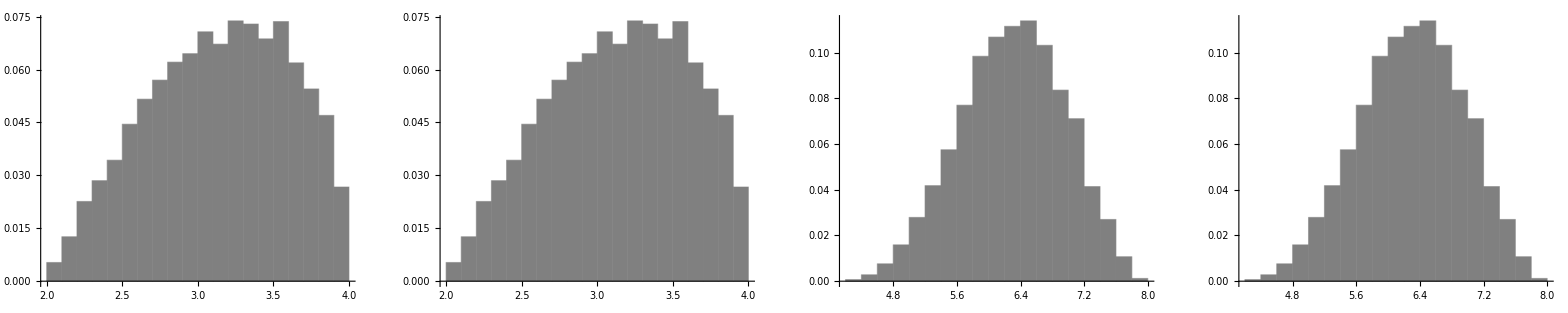

```mathematica
dist=BetaDistribution[2,1.5];
LMax[l1_,l2_]:=Max/@Transpose[{l1,l2}];
RV[lo_,hi_]:=lo+(hi-lo)RandomVariate[dist,10^4];
D1=RV[2,4];
D2=RV[4,7];
D3=RV[2,4];D4=RV[2,3];D5=RV[2,3];
S2=D1;
S3=D1;
S4=S3+D3;
S5=S3+D3;
H[V_]:=Histogram[V,Automatic,"Probability",AxesStyle->Directive[Black,4],ChartStyle->Directive[Gray]];
ROW1={H[S2],H[S3],H[S4],H[S5]};
GraphicsGrid[{ROW1}]
Cmax=LMax[LMax[S2+D2,S4+D4],S5+D5];Mean[Cmax]
```

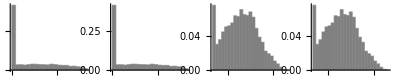

```mathematica
T2=ConstantArray[3.0,10^4];
T3=ConstantArray[3.0,10^4];
T4=ConstantArray[5.5,10^4];
T5=ConstantArray[5.5,10^4];

S2B=LMax[D1,T2];
S3B=LMax[D1,T3];
S4B=LMax[S3B+D3,T4];
S5B=LMax[S3B+D3,T5];
ROW2={H[S2B],H[S3B],H[S4B],H[S5B]};
GraphicsGrid[{ROW2}]
Cmax=LMax[LMax[S2B+D2,S4B+D4],S5B+D5];Mean[Cmax]
```

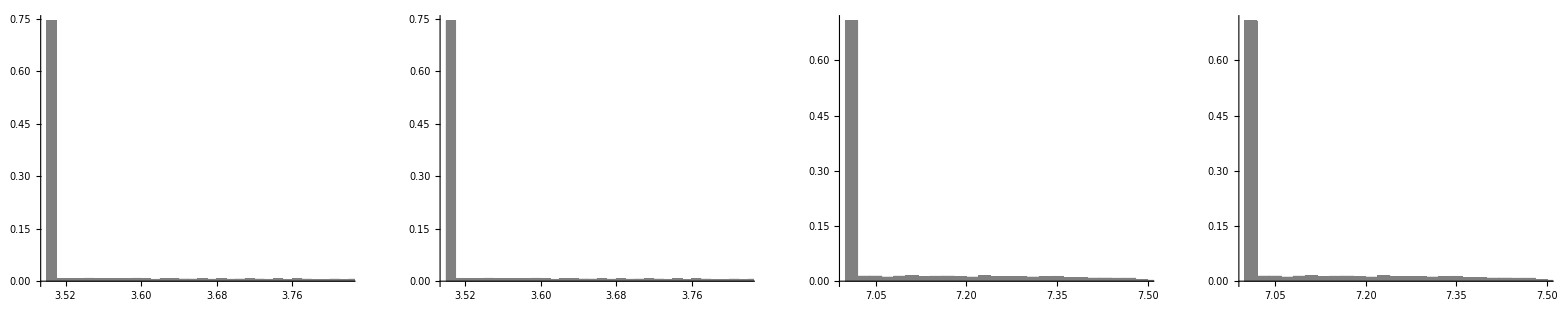

```mathematica
T2=ConstantArray[3.5,10^4];
T3=ConstantArray[3.5,10^4];
T4=ConstantArray[7.0,10^4];
T5=ConstantArray[7.0,10^4];

S2B=LMax[D1,T2];
S3B=LMax[D1,T3];
S4B=LMax[S3B+D3,T4];
S5B=LMax[S3B+D3,T5];
ROW2={H[S2B],H[S3B],H[S4B],H[S5B]};
GraphicsGrid[{ROW2}]
Cmax=LMax[LMax[S2B+D2,S4B+D4],S5B+D5];Mean[Cmax]
```

```mathematica
Export["/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/row4.eps",%373,"EPS"]
```

/home/ph/Dropbox/thesis-wrapper/chapter/prelim-2/row4.eps